```mathematica
(* Solving Newton's equations ddotx == 0, ddoty = -g gives *)
```

```mathematica
v0 = 20; g =9.81;
x[t_,θ_]:=Module[{},
t v0 Cos[θ]
]
y[t_,θ_]:=Module[{},
-g t^2/2 + v0 Sin[θ] t + 100
]
(* Time where the parabola hits the ground. *)
tint[θ_]:=Module[{},
(2 v0 Sin[θ]+√(800 g+4 v0^2 Sin[θ]^2))/(2 g)
]
```

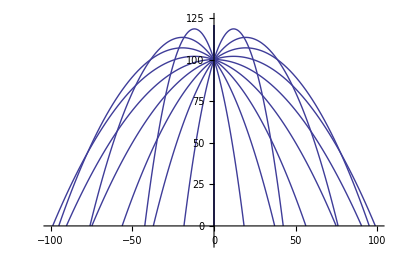

```mathematica
(* Make a plot of falling fireworks fragements *)
nm=10;
thvl=Pi Range[-nm,nm]/nm+Pi/2;
Show[Table[ParametricPlot[{x[t,thvl[[i]]],y[t,thvl[[i]]]},{t,0,tint[thvl[[i]]]},PlotRange->{{-100,100},{-10,125}}],{i,1,Length[thvl]}],PlotRange->{{-100,100},{-10,125}}]
```

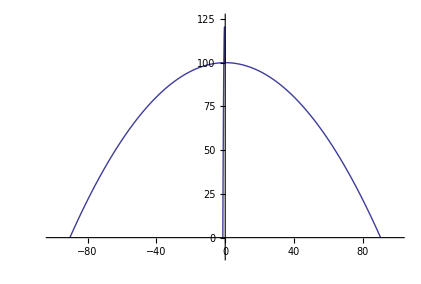

```mathematica
(* Plot of the fragments that have horizontal velocity vecs (and are the furthest from the point where the initial explosino occurred ) *)
nm=10;
thvl={0,Pi,Pi/2+0.01};
Show[Table[ParametricPlot[{x[t,thvl[[i]]],y[t,thvl[[i]]]},{t,0,tint[thvl[[i]]]},PlotRange->{{-100,100},{-10,125}}],{i,1,Length[thvl]}],PlotRange->{{-100,100},{-10,125}}]
```

```mathematica
(* Find the area under the base curve first using standard calculus.  Then find the lengths of the curves with θ between 0 and Pi from t = 0 until the intersect either the left or right curve.  Integrate over these arc lengths to find the upper area.  Finally find the area of the region by usuing rotation. s*)
```

```mathematica
bsecrv = {x[t,0],y[t,0]}
```

{20 t,100-4.905 t^2}

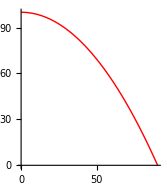

```mathematica
(* Do this for θ from 0 to Pi/2 .. note we only need half by symmetry. *)
g1=ParametricPlot[bsecrv,{t,0,tint[0]},PlotStyle->Red]
```

```mathematica
eqn={x[t,θ1],y[t,θ1]}-bsecrv
```

{-20 t+20 t Cos[θ1],0.+20 t Sin[θ1]}

```mathematica
crvint[θ_]:=(Cos[θ]-1)
```

```mathematica
θvls=Pi/2 Range[0,nm]/nm +Pi;
gr= Table[0,{i,1,Length[θvls]}];
For[i=1,i≤Length[gr],++i,
θvlstmp = θvls[[i]];
gr[[i]]=ParametricPlot[{x[t,θvlstmp],y[t,θvlstmp]},{t,0,crvint[θvlstmp]},PlotRange->{{0,60},{0,140}}];
]
```

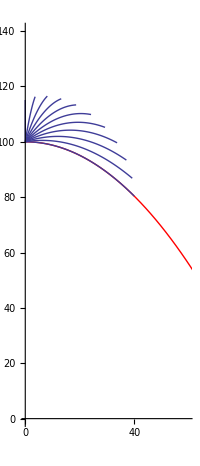

```mathematica
g1=ParametricPlot[bsecrv,{t,0,tint[0]},PlotStyle->Red,PlotRange->{{0,60},{0,140}}];
g2=Show[gr,PlotRange->{{0,60},{0,140}}];
Show[g1,g2]
```

```mathematica
(* Do this for θ from 0 to Pi/2 *)
```

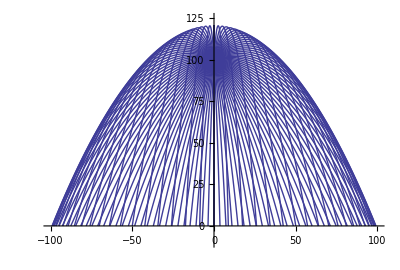

```mathematica
(* Another idea *) 
(* The envelope of the trajectories is traced out by the max of the y-values of the projectiles that vary over different θ values, as can be seen in the picture below.  Let's construct this function. *)
nm=50;
thvl=Pi Range[-nm,nm]/nm+Pi/2;
g1=Show[Table[ParametricPlot[{x[t,thvl[[i]]],y[t,thvl[[i]]]},{t,0,tint[thvl[[i]]]},PlotRange->{{-100,100},{-10,125}}],{i,1,Length[thvl]}],PlotRange->{{-100,100},{-10,125}}]
```

```mathematica
eqn=D[y[t,θ],t];
sol=Solve[eqn==0,t]
```

{{t→2.03874 Sin[θ]}}

```mathematica
x[sol[[1,1,2]],θ]
y[sol[[1,1,2]],θ]
```

40.7747 Cos[θ] Sin[θ]

100+20.3874 Sin[θ]^2

```mathematica
xfun[θ_]:=40.77471967380224 Cos[θ] Sin[θ]
maxfun[θ_]:=100+20.38735983690112 Sin[θ]^2
```

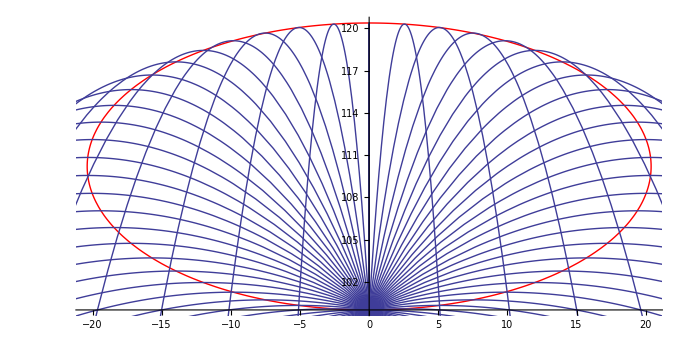

```mathematica
g2=ParametricPlot[{xfun[t],maxfun[t]},{t,0, Pi},PlotStyle->Red];
Show[g2,g1]
```

```mathematica
(* This shows that the max point is not the proper one to optimize! Instead let's try to optimize the max distance awa from our original point. *)
```

```mathematica
eqn=FullSimplify[D[x[t,θ]^2+y[t,θ]^2,t]];
sls=Solve[eqn==0,t];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
sls[[3]][[1,2]]
```

2.03874 Sin[θ]-((9.71534×10^-13-1.68275×10^-12 ⅈ) (-3.35479×10^13-3.4645×10^13 Sin[θ]^2))/(2.44949 √(-7.89233×10^8+7.25545×10^8 Cos[2. θ]-1.32435×10^8 Cos[4. θ])+36000. Sin[θ]-36000. Sin[θ]^3)^(1/3)+(0.0308719+0.0534717 ⅈ) (2.44949 √(-7.89233×10^8+7.25545×10^8 Cos[2. θ]-1.32435×10^8 Cos[4. θ])+36000. Sin[θ]-36000. Sin[θ]^3)^(1/3)

```mathematica
topt2[θ_]:=Re[2.038735983690112 Sin[θ]-((9.715339406949813*^-13-1.682746146561316*^-12 ⅈ) (-3.354790446*^13-3.4644996*^13 Sin[θ]^2))/(2.449489742783178 √(-7.89232841*^8+7.255449*^8 Cos[2. θ]-1.32435*^8 Cos[4. θ])+36000. Sin[θ]-36000. Sin[θ]^3)^(1/3)+(0.03087190949425993+0.05347171577072621 ⅈ) (2.449489742783178 √(-7.89232841*^8+7.255449*^8 Cos[2. θ]-1.32435*^8 Cos[4. θ])+36000. Sin[θ]-36000. Sin[θ]^3)^(1/3)]
```

```mathematica
{x[topt2[θ],θ],y[topt2[θ],θ]},
```

```mathematica
nm=10;
θ=Pi Range[0,nm]/nm+Pi/2;
g3=ParametricPlot[{x[topt2[θ],θ],y[topt2[θ],θ]},{θ,-Pi/2,Pi/2} ,PlotStyle->Red];
```

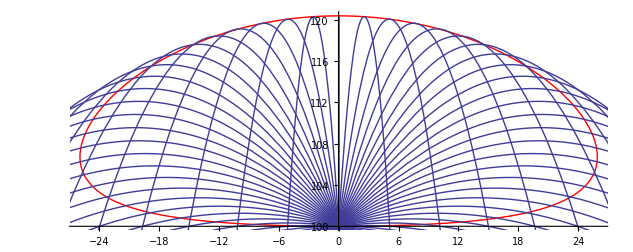

```mathematica
Show[g3,g1]
```

```mathematica
(* This idea is not going to work either! *)
```